```mathematica
fluent=Import["/home/beteix/Documents/PINN_from_beginning/Navier-Stokes/steady/fluent.csv"][[2;;,{2,3,5}]];
```

```mathematica
mixed=Import["/home/beteix/Documents/PINN_from_beginning/Navier-Stokes/steady/mixed.csv"][[2;;,{2,3,5}]];
```

```mathematica
fluent[[1000]]
```

{0.795,0.081,0.00147}

```mathematica
Max[fluent[[;;,3]]]
```

0.552

```mathematica
p1=ListContourPlot[fluent,AspectRatio->Automatic,ContourShading->None,Contours->Range[-0.5,0.5,0.025]];
```

```mathematica
p2=ListContourPlot[mixed,AspectRatio->Automatic,ContourShading->None,ContourStyle->Blue,Contours->Range[-0.5,0.5,0.025]];
```

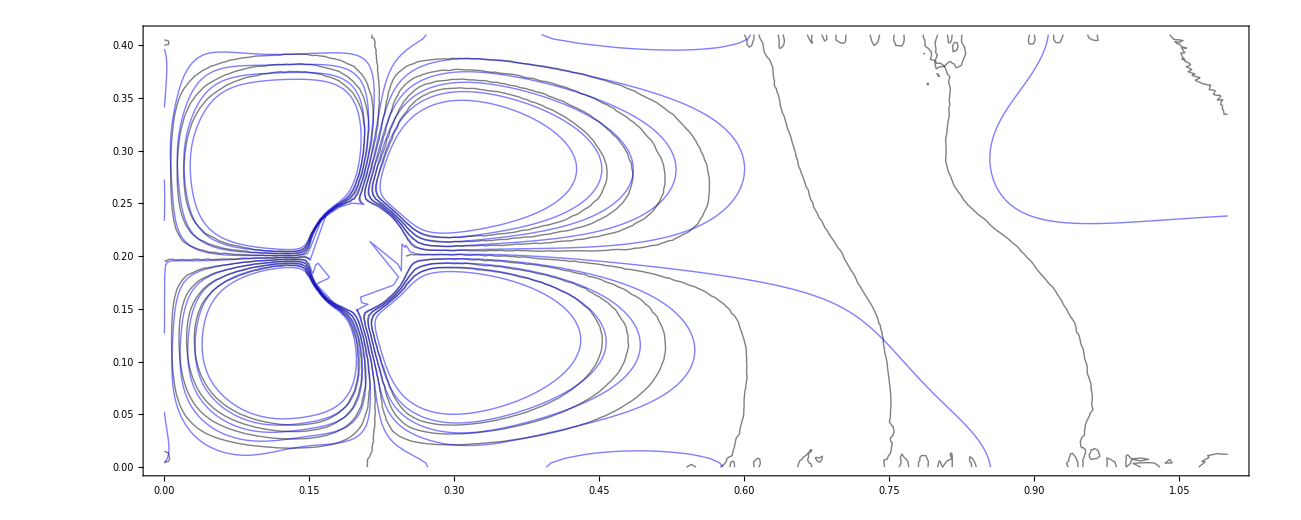

```mathematica
Show[p1,p2]
```